0.007445

S = 1.61182; Ns = 35; L = 1371.01

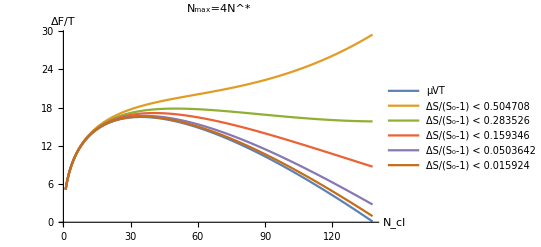

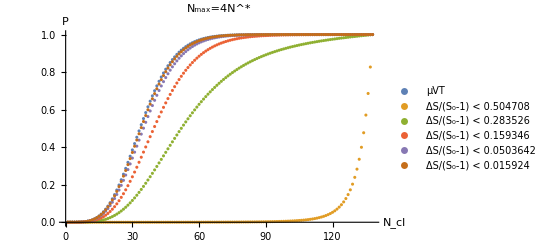

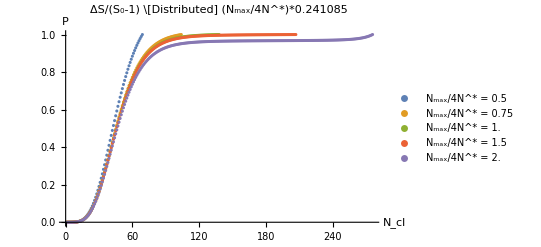

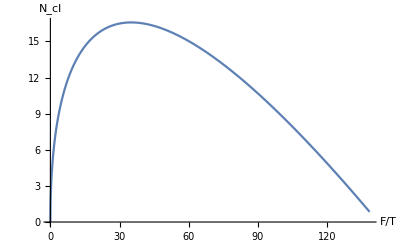

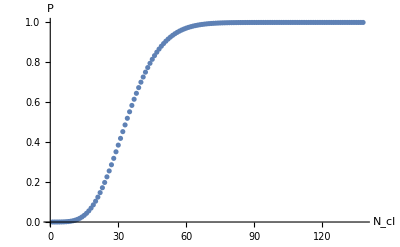

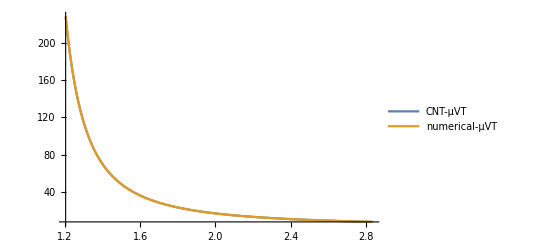

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ClearAll[sgmT,nCl,s0,nTotal,commErr,rhoB,rhoC];

g0[nCl_, sgmT_, s0_,nTotal_]:=sgmT*2*Sqrt[Pi*nCl]-nCl*Log[s0-nCl/nTotal];
nsFnc[sgmT_, s0_]:=(sgmT/Log[s0])^2*Pi;
nmaxFnc[sgmT_, s0_]:=4*nsFnc[sgmT, s0];
gMuVT[nCl_, sgmT_, s0_]:=Log[s0]*(2*Sqrt[nCl*nsFnc[sgmT, s0]]-nCl);
(*g[nCl_, sgmT_, s0_,nTotal_]:=gMuVT[nCl, sgmT, s0]-nCl*Log[1-nCl/nTotal/s0];*)
g[nCl_, sgmT_, s0_,nTotal_,rhoC_,rhoB_]:=gMuVT[nCl, sgmT, s0]-nCl*Log[(1-nCl/nTotal)/(1-s0*nCl/nTotal*rhoC/rhoB)];
(*g[nCl_, sgmT_, s0_,nTotal_,rhoC_,rhoB_]:=-nCl*Log[s0*(1-nCl/nTotal)/(1-s0*nCl/nTotal*rhoC/rhoB)]+2*sgmT*Sqrt[Pi*nCl/rhoB];*)
dg[nCl_, sgmT_, s0_,nTotal_,rhoC_,rhoB_]:=Module[{nmax=nmaxFnc[sgmT, s0]},g[nmax,sgmT,s0,nTotal,rhoC,rhoB]-gMuVT[nmax, sgmT, s0]];
lFnc[nTotal_,rhoC_,s0_]:=Sqrt[nTotal/rhoC/s0];
committorFnc[nMax_,gFnc_]:=
Module[{i,comm},
comm=Accumulate[Table[Exp[gFnc[i]]/i^(2/3),{i,1,nMax}]];
Table[{i,comm[[i]]/comm[[nMax]]},{i,1,nMax}]
]
(*committorFnc[nMax_,gFnc_]:=
Module[{i,comm},
comm=Accumulate[Table[Exp[gFnc[i]],{i,1,nMax}]];
Table[{i,comm[[i]]/comm[[nMax]]},{i,1,nMax}]
]*)
nSfromComm[nMaxLocal_,sgmTlocal_, s0local_, nTotalLocal_, rhoClocal_, rhoBlocal_]:=
Module[
{committorLocal, logCommInterp, nSlocal,nClLocal},
nSlocal=Round[nsFnc[sgmTlocal, s0local]];
committorLocal=committorFnc[nMaxLocal,g[#,sgmTlocal,s0local,nTotalLocal,rhoClocal,rhoBlocal]&];
logCommInterp =Interpolation[Table[{committorLocal[[i]][[1]],Log[committorLocal[[i]][[2]]]},{i,1,Length[committorLocal]}],InterpolationOrder->1];
nClLocal/.FindRoot[Abs[logCommInterp[nClLocal]-Log[0.5]],{nClLocal,nSlocal}]
];
commErr[sgmTlocal_, rhoClocal_,lLocal_,nMaxLocal_,phi1Data_,nSsdata_,dNsData_]:=
Module[
{nData,errList},
nData=Length[phi1Data];
errList=Table[Abs[(nSfromComm[nMaxLocal,sgmTlocal, (phi1Data[[i]]/rhoClocal), Round[phi1Data[[i]]*lLocal^2], rhoClocal, rhoB]-nSsdata[[i]])/dNsData[[i]]]^2,{i,1,nData}];
Total[errList]
];

phi1Data={0.0121, 0.0119, 0.0117, 0.01145, 0.0112, 0.0111};
nSsdata={29.28, 35.53, 35.9, 45.3, 49.9, 59.5};
dNsData={0.4, 0.9, 1.5, 2.0, 2.0, 3.0};
(*init guess*)
sgmT=0.915;
rhoC=0.00888;
(*phi2=0.01*)
sgmT=1.5847234867950104;
rhoC=0.0069238245600896555; (*from NVT-P1/2 fit*)
rhoC = 0.007445 (*from muVT at coexistance*)

s0 = 0.012 / rhoC;

rhoB=0.99;
nMaxFactor=1.0;
nTotalScale=2.0;

nData=Length[phi1Data];
nMax=Round[nmaxFnc[sgmT, s0]];
nS=Round[nsFnc[sgmT, s0]];
nTotal=Round[nMax/(s0-1)*10^nTotalScale];
l=lFnc[nTotal,rhoC,s0];

Print["S = ", s0,"; Ns = ",nS, "; L = ",l];

(*NMinimize[{Hold[commErr[sgmTlocal, rhoC*rhoCscale,320.0,100,phi1Data,nSsdata,dNsData]],sgmTlocal>0,rhoCscale>0},{sgmTlocal, rhoCscale},Method->{"Automatic","InitialPoints"->{{sgmT, 1.0}}}]*)

gFncs = {gMuVT[nCl, sgmT, s0]};
pNtotLists={committorFnc[nMax*nMaxFactor,gMuVT[#,sgmT,s0]&]};
gLbls = {"μVT"};
nTotalsScales = {0.5, 0.75,1.0,1.5,2.0};
nFfncs = Length[nTotalsScales];
nMaxLocal=Round[nMax*nMaxFactor];
For[i=1, i<=nFfncs, i++,
nTotalLocal=nMax/(s0-1)*10^nTotalsScales[[i]];
dSlocal=s0/(s0-1)*(1 - (1-nMaxLocal/nTotalLocal)/(1-s0*rhoC/rhoB*nMaxLocal/nTotalLocal));
AppendTo[gFncs,g[nCl,sgmT,s0,nTotalLocal,rhoC,rhoB]];
AppendTo[pNtotLists,committorFnc[nMaxLocal,g[#,sgmT,s0,nTotalLocal,rhoC,rhoB]&]];
AppendTo[gLbls,TraditionalForm[Style[Row[{"ΔS/(S_0-1) < ",dSlocal}]]]];
]
Plot[gFncs,{nCl,1, nMaxFactor*nMax},AxesLabel->{"N_cl","ΔF/T"},PlotLegends->gLbls,PlotLabel->"N_max=4N^*"]
ListPlot[pNtotLists,AxesLabel->{"N_cl","P"},PlotLegends->gLbls,PlotLabel->"N_max=4N^*"]

pNmaxLists = {};
pNmaxLbls={};
nMaxFactors={0.5,0.75,1.0,1.5,2.0};
nMaxLen=Length[nMaxFactors];
nTotalLocal=Round[nTotal*10^-1.175];
For[i=1,i<=nMaxLen,i++,
nMaxLocal=Round[nMax*nMaxFactors[[i]]];
dSlocal=s0/(s0-1)*(1 - (1-nMaxLocal/nTotalLocal)/(1-s0*rhoC/rhoB*nMaxLocal/nTotalLocal));
committorLocal=committorFnc[nMaxLocal,g[#,sgmT,s0,nTotalLocal,rhoC,rhoB]&];
AppendTo[pNmaxLists,Table[{committorLocal[[j]][[1]],committorLocal[[j]][[2]]},{j,1,Length[committorLocal]}]];AppendTo[pNmaxLbls,TraditionalForm[Style[Row[{"N_max/4N^* = ",nMaxFactors[[i]]}]]]];
];
ListPlot[pNmaxLists,AxesLabel->{"N_cl","P"},PlotLegends->pNmaxLbls,PlotRange->All,PlotLabel->TraditionalForm[Style[Row[{"ΔS/(S_0-1) \[Distributed] (N_max/4N^*)*",s0*nMax/nTotalLocal/(s0-1)}]]]]

Manipulate[Module[{nPointsLocal=100},
ListPlot[{Table[{phi1Data[[i]],Around[nSsdata[[i]],dNsData[[i]]]},{i,1,nData}],Table[{(rhoBulkMin+(rhoBulkMax-rhoBulkMin)*(i/nPointsLocal)),nSfromComm[nMaxLocal,sgmTlocal, ((rhoBulkMin+(rhoBulkMax-rhoBulkMin)*(i/nPointsLocal))/rhoClocal), Round[(rhoBulkMin+(rhoBulkMax-rhoBulkMin)*(i/nPointsLocal))*lLocal^2], rhoClocal, rhoB]},{i,0,nPointsLocal}],Table[{(rhoBulkMin+(rhoBulkMax-rhoBulkMin)*(i/nPointsLocal)),Pi*(sgmTlocal/Log[((rhoBulkMin+(rhoBulkMax-rhoBulkMin)*(i/nPointsLocal))/rhoClocal)])^2},{i,0,nPointsLocal}]},PlotRange->All,AxesLabel->{"ρ_bulk","N^*"},PlotLegends->{"NVT-data", "NVT-P_(1/2)","μVT-G_max"}]
],{{sgmTlocal,sgmT},sgmT/10,sgmT*10},
{{lLocal,320},120,10000},
{{rhoClocal,rhoC},0,0.011},
{{rhoBulkMin,0.011},rhoC,(1+(s0-1)*2)*rhoC},{{rhoBulkMax,0.01225},s0*rhoC,(1+(s0-1)*4)*rhoC},{{nMaxLocal, 100},50,1000}]

(*CNT vs P1/2 only*)
(*Manipulate[Module[{},
Plot[{Pi*(sgmTlocal/Log[(rhoBulkLocal/rhoClocal)])^2,nSfromComm[nMaxLocal,sgmTlocal, (rhoBulkLocal/rhoClocal), Round[rhoBulkLocal*lLocal^2], rhoClocal, rhoB]},{rhoBulkLocal,rhoBulkMin,rhoBulkMax},PlotRange->All,AxesLabel->{"rhoBulk","N*"},PlotLegends->{"CNT-muVT", "NVT-P1/2"}]
],{{sgmTlocal,sgmT},sgmT/10,sgmT*10},
{{lLocal,1000},120,10000},
{{rhoClocal,rhoC},0,0.011},
{{rhoBulkMin,0.011},rhoC,(1+(s0-1)*2)*rhoC},{{rhoBulkMax,0.01225},s0*rhoC,(1+(s0-1)*4)*rhoC},{{nMaxLocal, 120},50,1000}]*)
Manipulate[Module[{},
Plot[{Pi*(sgmTlocal/Log[(rhoBulkLocal/rhoClocal)])^2, nClLocal/.NMaximize[{g[nClLocal,sgmTlocal,(rhoBulkLocal/rhoClocal),Round[rhoBulkLocal*lLocal^2],rhoClocal,rhoB],nClLocal>=1},nClLocal,Method->{"Automatic","InitialPoints"->{{1.0},{2.0}}}][[2]],nSfromComm[nMaxLocal,sgmTlocal, (rhoBulkLocal/rhoClocal), Round[rhoBulkLocal*lLocal^2], rhoClocal, rhoB]},{rhoBulkLocal,rhoBulkMin,rhoBulkMax},PlotRange->All,AxesLabel->{"ρ_bulk","N^*"},PlotLegends->{"μVT-G_max", "NVT-G_max", "NVT-P_(1/2)"}]
],{{sgmTlocal,sgmT},sgmT/10,sgmT*10},
{{lLocal,320},120,10000},
{{rhoClocal,rhoC},0,0.011},
{{rhoBulkMin,0.011},rhoC,(1+(s0-1)*2)*rhoC},{{rhoBulkMax,0.01225},s0*rhoC,(1+(s0-1)*4)*rhoC},{{nMaxLocal, 100},50,1000}]
Manipulate[
Module[
{sgmTlocal=10^sgmTlocalLog,s0local=1+10^s0localLog,nTotalLocal,lLocal,nMaxLocal,
nClData={15., 20., 25., 30., 35., 40., 45., 50., 55., 60., 70., 82.},
commData={0.03214975, 0.18281835, 0.31413921, 0.46396839, 0.59692797, 0.69260011,
0.77262777, 0.82393501, 0.87820616, 0.89272295, 0.92936238, 0.97570756},
dCommData={0.00407713, 0.00485029, 0.02769334, 0.02458433, 0.01805506, 0.02811171,
0.01772728, 0.01559416, 0.01994103, 0.01425994, 0.01433598, 0.00799832},
nData
},
nData=Length[nClData];
nTotalLocal=Round[nmaxFnc[sgmTlocal, s0local]/(s0local-1)*10^nTotalLocalScale];
lLocal=Sqrt[nTotalLocal/rhoC/s0local];
nMaxLocal=Round[nMaxFactorLocal*nmaxFnc[sgmT, s0]];
ListPlot[{committorFnc[nMaxLocal,g[#,sgmTlocal,s0local,nTotalLocal,rhoC,rhoB]&],committorFnc[nMaxLocal,gMuVT[#,sgmTlocal,s0local]&],Table[{nClData[[i]],Around[commData[[i]],dCommData[[i]]]},{i,1,nData}]},AxesLabel->{"N_cl","P"},PlotLegends->{"NVT","μVT","NVT-data"},PlotLabel->TraditionalForm[Style[Row[{"N_total = ",nTotalLocal,"; L = ",lLocal}]]]]
],{{sgmTlocalLog,Log10[sgmT]},Log10[sgmT]-2,Log10[sgmT]+2},
{{s0localLog,Log10[s0-1]},Log10[s0-1]-2, Log10[s0-1]+2},
{{nTotalLocalScale,Log10[320^2*rhoC*s0/nmaxFnc[sgmT, s0]*(s0-1)]},0,4},{{nMaxFactorLocal,nMaxFactor},0.5,5}]
Manipulate[Module[{sgmTlocal=10^sgmTlocalLog,s0local=1+10^s0localLog,nTotalLocal,lLocal},
nTotalLocal=nmaxFnc[sgmTlocal, s0local]/(s0local-1)*10^nTotalLocalScale;
lLocal=Sqrt[nTotalLocal/rhoC/s0local];
Plot[{g[nCl,sgmTlocal,s0local,nTotalLocal,rhoC,rhoB],gMuVT[nCl, sgmTlocal, s0local]},{nCl,1, Round[nMaxFactor*nmaxFnc[sgmTlocal, s0local]]},PlotLegends->{"NVT","μVT"},AxesLabel->{"N_cl","ΔF/T"},PlotLabel->TraditionalForm[Style[Row[{"N_total = ",nTotalLocal,"; L = ",lLocal}]]]]],{{sgmTlocalLog,Log10[sgmT]},Log10[sgmT]-2,Log10[sgmT]+2},
{{s0localLog,Log10[s0-1]},Log10[s0-1]-2, Log10[s0-1]+2},
{{nTotalLocalScale,Log10[320^2*rhoC*s0/nmaxFnc[sgmT, s0]*(s0-1)]},0,4}]
Manipulate[Module[{sgmTlocal=10^sgmTlocalLog,s0local=1+10^s0localLog,nTotalMin,nmaxLocal,nTotalLocalScale1=0,nTotalLocalScale2=3,nTotalLocal1,nTotalLocal2},
nmaxLocal=nmaxFnc[sgmTlocal, s0local];
nTotalMin=nmaxLocal/(s0local-1);
nTotalLocal1=nTotalMin*10^nTotalLocalScale1;
nTotalLocal2=nTotalMin*10^nTotalLocalScale2;
ParametricPlot[{Log10[nTotalLocal],dg[nmaxLocal,sgmTlocal,s0local,nTotalLocal,rhoC,rhoB]},{nTotalLocal,nTotalLocal1,nTotalLocal2},PlotRange->All,AspectRatio->Abs[dg[nmaxLocal,sgmTlocal,s0local,nTotalLocal2,rhoC,rhoB]-dg[nmaxLocal,sgmTlocal,s0local,nTotalLocal1,rhoC,rhoB]]/Abs[Log10[lFnc[nTotalLocal2,rhoC,s0local]/lFnc[nTotalLocal1,rhoC,s0local]]]/4,AxesLabel->{TraditionalForm[Style[Row[{HoldForm[Log10[Subscript[N, total]]]}]]],"ΔF(4N^*)/T"}]],{{sgmTlocalLog,Log10[sgmT]},Log10[sgmT]-2,Log10[sgmT]+2},
{{s0localLog,Log10[s0-1]},Log10[s0-1]-2, Log10[s0-1]+2}]
Manipulate[Module[{sgmTlocal=10^sgmTlocalLog,s0local=1+10^s0localLog,nTotalMin,nmaxLocal,nTotalLocalScale1=0,nTotalLocalScale2=3,nTotalLocal1,nTotalLocal2},
nmaxLocal=nmaxFnc[sgmTlocal, s0local];
nTotalMin=nmaxLocal/(s0local-1);
nTotalLocal1=nTotalMin*10^nTotalLocalScale1;
nTotalLocal2=nTotalMin*10^nTotalLocalScale2;
ParametricPlot[{Log10[Sqrt[nTotalLocal / rhoC / s0local]],Log10[dg[nmaxLocal,sgmTlocal,s0local,nTotalLocal,rhoC,rhoB]]},{nTotalLocal,nTotalLocal1,nTotalLocal2},PlotRange->All,AspectRatio->Abs[Log10[dg[nmaxLocal,sgmTlocal,s0local,nTotalLocal2,rhoC,rhoB]/dg[nmaxLocal,sgmTlocal,s0local,nTotalLocal1,rhoC,rhoB]]]/Abs[Log10[lFnc[nTotalLocal2,rhoC,s0local]/lFnc[nTotalLocal1,rhoC,s0local]]]/2,AxesLabel->{TraditionalForm[Style[Row[{HoldForm[Log10[L]]}]]],TraditionalForm[Style[Row[{HoldForm[Log10[ΔF[4 SuperStar[N]]/T]]}]]]}]],{{sgmTlocalLog,Log10[sgmT]},Log10[sgmT]-2,Log10[sgmT]+2},
{{s0localLog,Log10[s0-1]},Log10[s0-1]-2, Log10[s0-1]+2}]

Plot[g[nCl,sgmT,s0,nTotal,rhoC,rhoB],{nCl,0, nmaxFnc[sgmT, s0]},AxesLabel->{"F/T",TraditionalForm[Style[Row[{HoldForm[Subscript[N, cl]]}]]]}]
ListPlot[committorFnc[Round[nMaxFactor*nMax],gMuVT[#,sgmT,s0]&],AxesLabel->{"N_cl","P"}]
nSnvt=NMaximize[{gMuVT[nCl,sgmT,s0],nCl>=1},nCl,Method->{"Automatic","InitialPoints"->{{1.0},{2.0}}}];
Plot[{Pi*(sgmT/Log[s0local])^2, nCl/.NMaximize[{gMuVT[nCl,sgmT,s0local],nCl>=1},nCl,Method->{"Automatic","InitialPoints"->{{1.0},{2.0}}}][[2]]},{s0local,1+(s0-1)/3,1+(s0-1)*3},PlotRange->All,PlotLegends->{"CNT-μVT", "numerical-μVT"}]
```

```mathematica
ClearAll[sgmT, s0,nTotal,rhoC,rhoB];
ass={sgmT>0,s0>1,nTotal>0,rhoC>0,rhoB>rhoC};
gPrime=FullSimplify[D[g[nCl, sgmT, s0,nTotal,rhoC,rhoB],nCl],Assumptions->ass]
gPrime1=Normal[FullSimplify[Series[gPrime,{nTotal,Infinity,2}],Assumptions->ass]]
FullSimplify[Solve[gPrime1==0,nCl,Assumptions->ass],Assumptions->ass]
```

nTotal (1/(-nCl+nTotal)+rhoB/(-nTotal rhoB+nCl rhoC s0))+(√π sgmT)/(√nCl)-Log[((nCl-nTotal) rhoB s0)/(-nTotal rhoB+nCl rhoC s0)]

(2 nCl (rhoB-rhoC s0))/(nTotal rhoB)+(3 nCl^2 (rhoB-rhoC s0) (rhoB+rhoC s0))/(2 nTotal^2 rhoB^2)+(√π sgmT)/(√nCl)-Log[s0]

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{nCl→Root[-4 nTotal^4 π rhoB^4 sgmT^2+4 nTotal^4 rhoB^4 Log[s0]^2 #1+(-16 nTotal^3 rhoB^4 Log[s0]+16 nTotal^3 rhoB^3 rhoC s0 Log[s0]) #1^2+(16 nTotal^2 rhoB^4-32 nTotal^2 rhoB^3 rhoC s0+16 nTotal^2 rhoB^2 rhoC^2 s0^2-12 nTotal^2 rhoB^4 Log[s0]+12 nTotal^2 rhoB^2 rhoC^2 s0^2 Log[s0]) #1^3+(24 nTotal rhoB^4-24 nTotal rhoB^3 rhoC s0-24 nTotal rhoB^2 rhoC^2 s0^2+24 nTotal rhoB rhoC^3 s0^3) #1^4+(9 rhoB^4-18 rhoB^2 rhoC^2 s0^2+9 rhoC^4 s0^4) #1^5&,1]},{nCl→Root[-4 nTotal^4 π rhoB^4 sgmT^2+4 nTotal^4 rhoB^4 Log[s0]^2 #1+(-16 nTotal^3 rhoB^4 Log[s0]+16 nTotal^3 rhoB^3 rhoC s0 Log[s0]) #1^2+(16 nTotal^2 rhoB^4-32 nTotal^2 rhoB^3 rhoC s0+16 nTotal^2 rhoB^2 rhoC^2 s0^2-12 nTotal^2 rhoB^4 Log[s0]+12 nTotal^2 rhoB^2 rhoC^2 s0^2 Log[s0]) #1^3+(24 nTotal rhoB^4-24 nTotal rhoB^3 rhoC s0-24 nTotal rhoB^2 rhoC^2 s0^2+24 nTotal rhoB rhoC^3 s0^3) #1^4+(9 rhoB^4-18 rhoB^2 rhoC^2 s0^2+9 rhoC^4 s0^4) #1^5&,2]},{nCl→Root[-4 nTotal^4 π rhoB^4 sgmT^2+4 nTotal^4 rhoB^4 Log[s0]^2 #1+(-16 nTotal^3 rhoB^4 Log[s0]+16 nTotal^3 rhoB^3 rhoC s0 Log[s0]) #1^2+(16 nTotal^2 rhoB^4-32 nTotal^2 rhoB^3 rhoC s0+16 nTotal^2 rhoB^2 rhoC^2 s0^2-12 nTotal^2 rhoB^4 Log[s0]+12 nTotal^2 rhoB^2 rhoC^2 s0^2 Log[s0]) #1^3+(24 nTotal rhoB^4-24 nTotal rhoB^3 rhoC s0-24 nTotal rhoB^2 rhoC^2 s0^2+24 nTotal rhoB rhoC^3 s0^3) #1^4+(9 rhoB^4-18 rhoB^2 rhoC^2 s0^2+9 rhoC^4 s0^4) #1^5&,3]},{nCl→Root[-4 nTotal^4 π rhoB^4 sgmT^2+4 nTotal^4 rhoB^4 Log[s0]^2 #1+(-16 nTotal^3 rhoB^4 Log[s0]+16 nTotal^3 rhoB^3 rhoC s0 Log[s0]) #1^2+(16 nTotal^2 rhoB^4-32 nTotal^2 rhoB^3 rhoC s0+16 nTotal^2 rhoB^2 rhoC^2 s0^2-12 nTotal^2 rhoB^4 Log[s0]+12 nTotal^2 rhoB^2 rhoC^2 s0^2 Log[s0]) #1^3+(24 nTotal rhoB^4-24 nTotal rhoB^3 rhoC s0-24 nTotal rhoB^2 rhoC^2 s0^2+24 nTotal rhoB rhoC^3 s0^3) #1^4+(9 rhoB^4-18 rhoB^2 rhoC^2 s0^2+9 rhoC^4 s0^4) #1^5&,4]},{nCl→Root[-4 nTotal^4 π rhoB^4 sgmT^2+4 nTotal^4 rhoB^4 Log[s0]^2 #1+(-16 nTotal^3 rhoB^4 Log[s0]+16 nTotal^3 rhoB^3 rhoC s0 Log[s0]) #1^2+(16 nTotal^2 rhoB^4-32 nTotal^2 rhoB^3 rhoC s0+16 nTotal^2 rhoB^2 rhoC^2 s0^2-12 nTotal^2 rhoB^4 Log[s0]+12 nTotal^2 rhoB^2 rhoC^2 s0^2 Log[s0]) #1^3+(24 nTotal rhoB^4-24 nTotal rhoB^3 rhoC s0-24 nTotal rhoB^2 rhoC^2 s0^2+24 nTotal rhoB rhoC^3 s0^3) #1^4+(9 rhoB^4-18 rhoB^2 rhoC^2 s0^2+9 rhoC^4 s0^4) #1^5&,5]}}

```mathematica
{1,2,3}/3
```

{1/3,2/3,1}

```mathematica
0.006777376188790738*1.0216084170657564
```

0.00692382

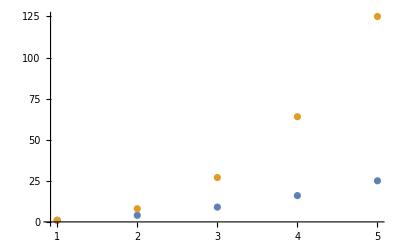

```mathematica
ListPlot[{Table[{x,x^2},{x,1,5}],Table[{x,x^3},{x,1,5}]}]
```

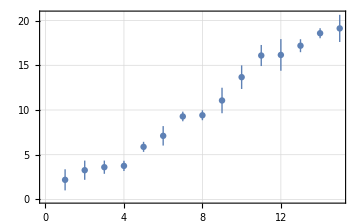

```mathematica
ListPlot[{Around[2.1918723516632497,1.179010739030292],Around[3.269299346380361,1.073705635691565],Around[3.6053592738851457,0.739163395566707],Around[3.7514153078736783,0.5725226059893145],Around[5.879896586647565,0.5619792915867954],Around[7.112362343363362,1.0879608947420247],Around[9.278795054867082,0.5373109058942613],Around[9.412233486731921,0.5535868197885279],Around[11.065052397750446,1.4257364416193785],Around[13.672151847810191,1.3195436837073276],Around[16.09335699120726,1.178224868004306],Around[16.157357493627416,1.7698593032864212],Around[17.190308584936687,0.7243113209289365],Around[18.58412891002442,0.5599838391809948],Around[19.126038249375526,1.5202600663945063]},Sequence[PlotTheme->"Detailed",ImageSize->Medium]]
```

```mathematica
nsFnc[sgmT, s0]*4
```

104.349